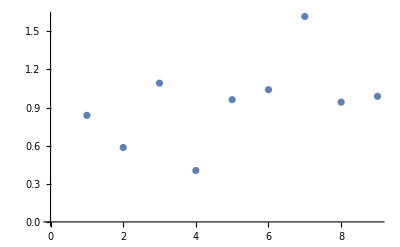

```mathematica
ListPlot[Table[Log2[newTimes[[i]]]-Log2[newTimes[[i-1]]],{i,2,10}]]
```

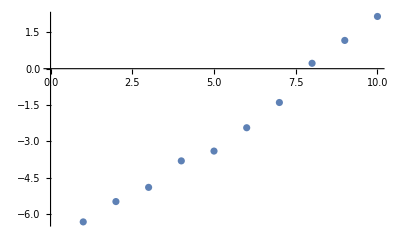

```mathematica
ListPlot[newTimes//Log2]
```

```mathematica
timesFull=Table[Timing[fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{n,n}]]⟦1⟧,{n,1,6}]
```

{0.001292,0.00327,0.01276,0.051585,0.329723,2.7101}

```mathematica
timesSparse=Table[Timing[sparseCoefficients[Sin[Pi #[[1]]+#[[2]]]&,n,2]]⟦1⟧,{n,1,10}]
```

{0.001067,0.001943,0.00388,0.007949,0.015966,0.042169,0.091727,0.169797,0.853202,3.27109}

```mathematica
Timing[sparseCoefficients[Sin[Pi #[[1]]+#[[2]]]&,11,2]]⟦1⟧
```

```mathematica
AppendTo[timesSparse,20.429212]
```

{0.001067,0.001943,0.00388,0.007949,0.015966,0.042169,0.091727,0.169797,0.853202,3.27109,20.4292}

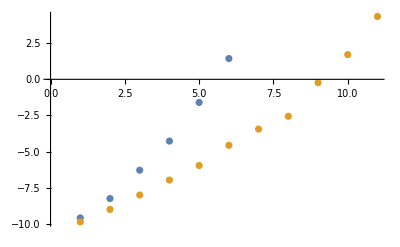

```mathematica
ListPlot[{timesFull,timesSparse}//Log2]
```

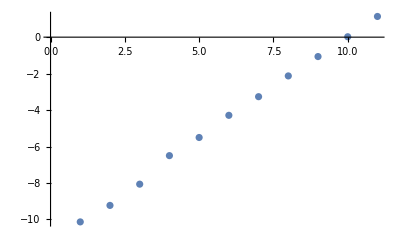

```mathematica
Table[Timing[sparseCoefficients2D[Sin[Pi #1+#2]&,n]][[1]],{n,1,11}]//Log2//ListPlot
```

```mathematica
hiterateTimes=Table[Timing[hierIterate[{n,n}]]⟦1⟧,{n,1,10}];
siterateTimes=Table[Timing[sparseIterate[n,2]]⟦1⟧,{n,1,14}];
```

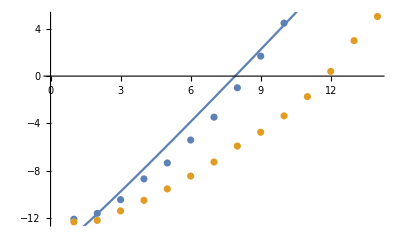

```mathematica
Show[ListPlot[{hiterateTimes,siterateTimes}//Log2],Plot[{x Log[Log[100x]]-15},{x,0,14}]]
```